```mathematica
Id=PauliMatrix[0];X=PauliMatrix[1];Y=PauliMatrix[2];Z=PauliMatrix[3];
```

```mathematica
Define the reference assemblage elements as σax and corresponding normalized states as ρax
```

```mathematica
σ00=(Id+Z)/4;σ10=(Id-Z)/4;σ01=(Id+X)/4;σ11=(Id-X)/4;
ρ00=(Id+Z)/2; ρ10=(Id-Z)/2; ρ01=(Id+X)/2 ; ρ11=(Id-X)/2;
```

```mathematica
Define Bob' s operators and Tax
```

```mathematica
B0 = Cos[θ]Z+Sin[θ]X; B1 = Cos[θ]Z-Sin[θ]X;
T00 = B0+B1; T10 = -T00; T01=B0-B1 ; T11=-T01;
```

```mathematica
Define the extraction map
```

```mathematica
Λ[ρ_,c_,Γ_]:=FullSimplify[((1+c)/2) ρ+((1-c)/2) Dot[Γ,ρ,Γ]]
```

```mathematica
1. Inequalities in the first interval
```

```mathematica
K00=Λ[ρ00,c,Z]; K10=Λ[ρ10,c,Z]; K01=Λ[ρ01,c,Z]; K11=Λ[ρ11,c,Z];
```

```mathematica
Reduce[And@@Join[Thread[Eigenvalues[K00-s T00- t0 Id ]≥0],{1≥c≥-1},{Pi/4≥θ≥0}],{t0},Reals]
```

(-1≤c≤1&&0≤θ≤π/4&&s<Sec[θ]/4&&t0≤2 s Cos[θ])||(-1≤c≤1&&0≤θ≤π/4&&s≥Sec[θ]/4&&t0≤1-2 s Cos[θ])

```mathematica
Reduce[And@@Join[Thread[Eigenvalues[K11-s T11- t1 Id ]≥0],{1≥c≥-1},{Pi/4≥θ≥0}],{t1},Reals]
```

(θ==0&&((-1≤c≤0&&t1≤(1+c)/2)||(0<c≤1&&t1≤(1-c)/2)))||(0<θ≤π/4&&-1≤c≤1&&((s<1/4 c Csc[θ]&&t1≤1/2 (1-c+4 s Sin[θ]))||(s≥1/4 c Csc[θ]&&t1≤1/2 (1+c-4 s Sin[θ]))))

```mathematica
Optimize t over all measurements
```

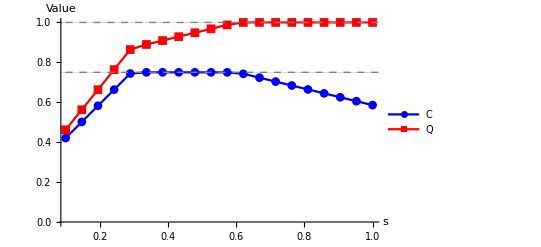

```mathematica
sValues=Subdivide[0.1,1,19];
results=Table[Module[{c,t,classicalbound,quantumbound},c=Min[1,4s Sin[θ]];
t=(NMinValue[{Min[1-2s*Cos[θ],2 s*Cos[θ]]+Min[(1/2)*(1+c-4s*Sin[θ]),(1/2)*(1-c+4s*Sin[θ])],Pi/4≥θ≥0},θ]);
classicalbound=N[s+t/2];
quantumbound=N[√2 s+t/2];
{s,classicalbound,quantumbound}],{s,sValues}];

(*Create two lists for plotting*)
data1=results[[All,{1,2}]];
data2=results[[All,{1,3}]];

(*Plot both expressions along with horizontal lines at 1 (maximum fidelity) and 0.85 (trivial bound)*)
Show[ListLinePlot[{data1,data2},PlotLegends->{"C","Q"},PlotMarkers->Automatic,PlotStyle->{Blue,Red},AxesLabel->{"s","Value"},PlotRange->All,GridLines->{None,{0.75,1}}],Graphics[{Dashed,Gray,Line[{{0.1,1},{15,1}}],Line[{{0.1,0.75},{15,0.75}}]}]]
```

```mathematica
1. Inequalities in the second interval
```

```mathematica
K00b=Λ[ρ00,c,X]; K10b=Λ[ρ10,c,X]; K01b=Λ[ρ01,c,X]; K11b=Λ[ρ11,c,X];
```

```mathematica
Reduce[And@@Join[Thread[Eigenvalues[K00b-s T00- t0 Id ]≥0],{1≥c≥-1},{Pi/2≥θ>Pi/4}],{t0},Reals]
```

(π/4<θ<π/2&&-1≤c≤1&&((s<1/4 c Sec[θ]&&t0≤1/2 (1-c+4 s Cos[θ]))||(s≥1/4 c Sec[θ]&&t0≤1/2 (1+c-4 s Cos[θ]))))||(θ==π/2&&((-1≤c≤0&&t0≤(1+c)/2)||(0<c≤1&&t0≤(1-c)/2)))

```mathematica
Reduce[And@@Join[Thread[Eigenvalues[K11b-s T11- t1 Id ]≥0],{1≥c≥-1},{Pi/2≥θ>Pi/4}],{t1},Reals]
```

(-1≤c≤1&&π/4<θ≤π/2&&s<Csc[θ]/4&&t1≤2 s Sin[θ])||(-1≤c≤1&&π/4<θ≤π/2&&s≥Csc[θ]/4&&t1≤1-2 s Sin[θ])

```mathematica
sValues=Subdivide[0.1,1,19];
results=Table[Module[{c,t,expr1,expr2},c=Min[1,4s Cos[θ]];
t=(NMinValue[{Min[1-2s*Sin[θ],2 s*Sin[θ]]+Min[(1/2)*(1+c-4s*Cos[θ]),(1/2)*(1-c+4s*Cos[θ])],Pi/4<θ≤Pi/2},θ]);
classicalbound=N[s+t/2];
quantumbound=N[√2 s+t/2];
{s,classicalbound,quantumbound}],{s,sValues}];


(*Create two lists for plotting*)
data1=results[[All,{1,2}]];
data2=results[[All,{1,3}]];

(*Plot both expressions along with horizontal lines at 1 (maximum fidelity) and 0.85 (trivial bound)*)
Show[ListLinePlot[{data1,data2},PlotLegends->{"C","Q"},PlotMarkers->Automatic,PlotStyle->{Blue,Red},AxesLabel->{"s","Value"},PlotRange->All,GridLines->{None,{0.75,1}}],Graphics[{Dashed,Gray,Line[{{0.1,1},{15,1}}],Line[{{0.1,0.75},{15,0.75}}]}]]
```

-Graphics-